### Qubit mapping in a Bloch sphere

```mathematica
vectorBloch[theta_,phi_]:= Graphics3D[
{Red,(*Thickness[0.01],*)Cylinder[{{0,0,0},0.8Dynamic@{Sin[theta] Cos[phi],Sin[theta]Sin[phi],Cos[theta]}},.02]},
Line[{{0,0,1},{0,0,-1}}],
Line[{{1,0,0},{-1,0,0}}],Boxed->False,Axes->False,ImageSize->450] (*unit Bloch vector*)

xyz=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2 π},PlotStyle->{{Black,Thick,Dashed},{Black,Thick,Dashed},{Black,Thick,Dashed}},Boxed->False,Axes->False,ImageSize->450];

xyz0[phi_]:=ParametricPlot3D[{{Cos[phi]Sin[t], Sin[phi]Sin[t],Cos[t] }},{t,0,2 π},PlotStyle->{Red,Opacity[0.5],Thick,Dashed},Boxed->False,Axes->False,ImageSize->450,Mesh->None];

pl[theta_,phi_]:=
Row[{Framed[ Style[{"θ ="<>ToString[NumberForm[theta,{4,3}]], "ϕ ="<>ToString[NumberForm[phi,{4,3}]]},16],Background->Lighter[Gray,0.95] ],
 Framed[ Style["|qubit⟩="<>ToString[NumberForm[{{Cos[theta/2]},{ⅇ^(ⅈ phi)Sin[theta/2]}}//Chop,{4,3}]//TraditionalForm],16],Background->Lighter[Gray,0.95] ]}," "]

poincareBloch[theta_,phi_]:=
Graphics3D[{Opacity[0.1],Sphere[],Black,Thick,Opacity[1.],
PointSize[.02],Point[{0,0,0}],Point[{1,0,0}],Point[{-1,0,0}],Point[{0,1,0}],Point[{0,-1,0}],Point[{0,0,1}],Point[{0,0,-1}],
Line[{{0,1,0},{0,-1,0}}],
Line[{{0,0,1},{0,0,-1}}],
Line[{{1,0,0},{-1,0,0}}],
Line[{{0.8Sin[theta] Cos[phi],0.8Sin[theta]Sin[phi],0.8Cos[theta]},{0.8Sin[theta] Cos[phi],0.8Sin[theta]Sin[phi],0}}],
Line[{{0.8Sin[theta] Cos[phi],0,0},{0.8Sin[theta] Cos[phi],0.8Sin[theta]Sin[phi],0}}],
Line[{{0,0.8Sin[theta]Sin[phi],0},{0.8Sin[theta] Cos[phi],0.8Sin[theta]Sin[phi],0}}],
Text[Style[Row[{"|0⟩=",MatrixForm[{1,0}]}], 14,Bold], {0,0,1.3 }],
Text[Style[Row[{"|1⟩=",MatrixForm[{0,1}]}], 14,Bold], {0,0,-1.3 }],
Text[Style[Row[{"1/(√2)",MatrixForm[{1,ⅈ}]}], 14,Bold], {0,1.3 ,0}],
Text[Style[Row[{"1/(√2)",MatrixForm[{1,-ⅈ}]}], 14,Bold],{0,-1.3 ,0}],
Text[Style[Row[{"1/(√2)",MatrixForm[{1,1}]}], 14,Bold], {1.6 ,-0.25,0}],
Text[Style[Row[{"1/(√2)",MatrixForm[{1,-1}]}],14,Bold],{-1.5 ,0.3,0}],
Boxed->False,Axes->False,ImageSize->450}]
```

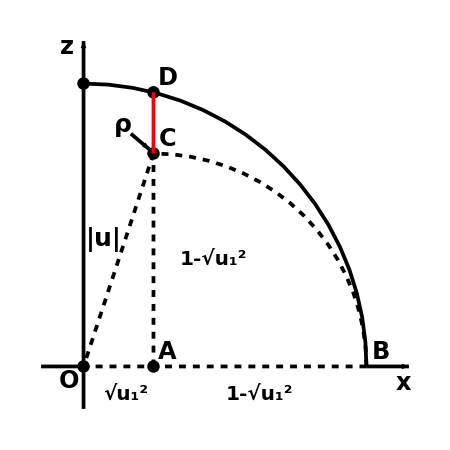

```mathematica
d={Pi/10,Pi/3};
thickness=0.006;
{theta,phi}=d;
u1=0.8Sin[theta] Cos[phi];
u2=0.8Sin[theta]Sin[phi];
u12=√(u1^2+u2^2);
f2a=Graphics[{Thickness[thickness],Circle[{0,0},1,{0,Pi/2}],Dashed,Circle[{u12,0},1-u12,{0,Pi/2}],Line[{{1,0},{0,0}}],Line[{{u12,0},{u12,1-u12}}],Line[{{u12,1-u12},{0,0}}],PointSize[.02],Point[{u12,1-u12}],Point[{0,0}],Point[{u12,0}],Point[{u12,√(1-u12^2)}],Point[{0,1}],Text[Style["ρ",25,Bold], {.138,0.855 }],(*Text[Style["|u|",25,Bold], {-.03,0.45}],*)Text[Style["|u|",25,Bold], {.07,0.45}],Text[Style["O",24,Bold], {-0.05,-0.05}],Text[Style["A",24,Bold], {u12+0.05,0.05}],Text[Style["B",24,Bold], {1+0.05,0.05}],Text[Style["C",24,Bold], {u12+0.05,1-u12+0.05}],Text[Style["D",24,Bold], {u12+0.05,√(1-u12^2)+0.05}],Text[Style["x",24,Bold], {1.13,-0.06}],Text[Style["z",24,Bold], {-0.06,1.13}],Text[Style["1-√(u_1^2)",20,Bold], {.46,0.38}],Text[Style["1-√(u_1^2)",20,Bold], {.62,-0.1}],,Text[Style["√(u_1^2)",20,Bold], {.15,-0.1}]},ImageSize->{450,450}];
f2b=Graphics[{Thickness[thickness],Red,Line[{{u12,1-u12},{u12,√(1-u12^2)}}]},ImageSize->{450,450}];
f3b=Graphics[{Thickness[thickness],Arrow[{{1,0},{1.15,0}}],Arrow[{{u12-0.08,1-u12+0.07},{u12-0.015,1-u12+0.015}}],Arrow[{{0,-0.15},{0,1.15}}],Line[{{-0.15,0},{0,0}}]}];
f2=Show[f2a,f2b,f3b]
```

### Shadow area

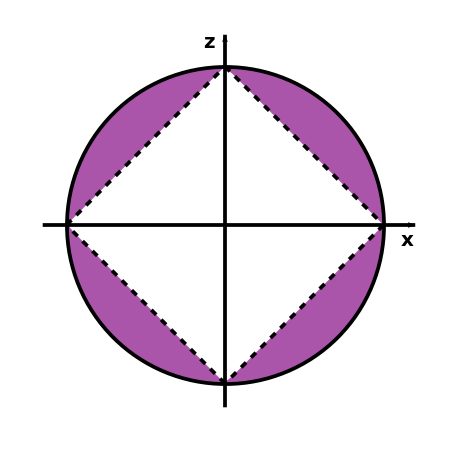

```mathematica
cleanContourPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,_Tooltip,Infinity];
Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]]

cleanContourPlot[Legended[cp_Graphics,rest___]]:=Legended[cleanContourPlot[cp],rest];
xmax=1.16;
ymax=1.16;
m1=ContourPlot[0.6,{x,-xmax,xmax},{y,-ymax,ymax},ColorFunction->(If[#<1,Lighter[Purple],Lighter[Red,#]]&),RegionFunction->Function[{x,y,z},x^2+y^2<1&&Abs[x]+Abs[y]>1],Frame->None,ImageSize->{450,450}];
m1=cleanContourPlot[m1];
m1a=DensityPlot[0.6,{x,-xmax,xmax},{y,-ymax,ymax},RegionFunction->Function[{x,y,z},x^2+y^2<1&&Abs[x]+Abs[y]>1],Frame->None];
m2=Graphics[{Thickness[thickness],Circle[],Arrow[{{-1.15,0},{1.2,0}}],Arrow[{{0,-1.15},{0,1.2}}],Text[Style["x",20,Bold], {1.15,-0.1}],Text[Style["z",20,Bold], {-0.1,1.15}]},ImageSize->{450,450}];
(*(*m3a*)=ContourPlot[Abs[x]+Abs[y]==1,{x,-xmax,xmax},{y,-ymax,ymax}];*)
m3=Graphics[{Thickness[thickness],Black,Dashed,Line[{{-1,0},{0,1}}],Line[{{0,1},{1,0}}],Line[{{1,0},{0,-1}}],Line[{{0,-1},{-1,0}}]},ImageSize->{450,450}];
mm=Show[m1,m2,m3]
```

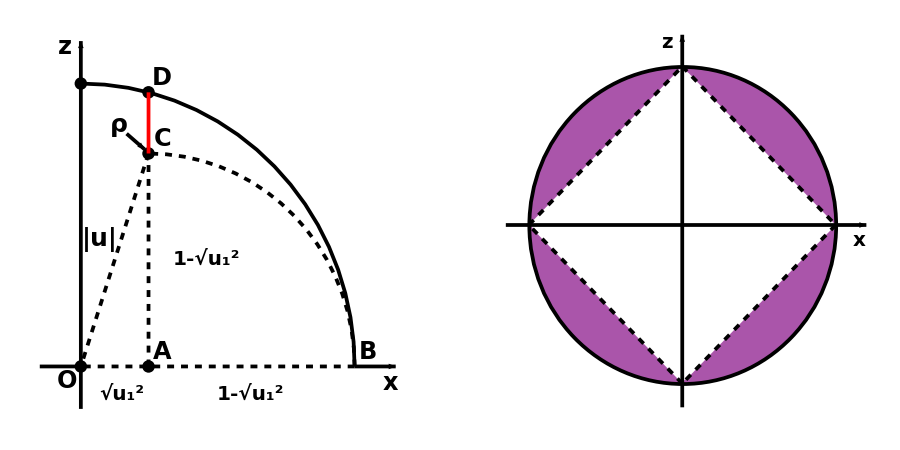

```mathematica
dim2a=GraphicsGrid[{{f2,mm}},ImageSize->{900,450}]
```

```mathematica
Export["E:\\06_Coh\\00_Code\\01_Plot_qubit\\00_Figures\\00_20191022d_dim2_app.eps",dim2a]
```

E:\06_Coh\00_Code\01_Plot_qubit\00_Figures\00_20191022d_dim2_app.eps

```mathematica
"E:\\06_Coh\\00_Code\\01_Plot_qubit\\00_Figures\\00_20191022c_dim2_app.eps"
```